```mathematica
Clear["Global`*"]
```

```mathematica
ssh[n_,u_,v_,w_,g_]:=(H=ConstantArray[0,{2n,2n}];
A=ConstantArray[0,2n]; B=ConstantArray[0,2n];
{A[[2]], A[[4]], A[[2n]]}={u-g,w,v};
{B[[1]], B[[3]], B[[2n-1]]}={u+g,v,w};
Do[H[[2i+1]]=RotateRight[A,2 i],{i,0,n-1} ];
Do[H[[2i]]=RotateRight[B, 2(i-1)],{i,1,n} ];
{H[[1,2n]],H[[2,2n-1]],H[[2n-1,2]],H[[2n,1]]}={0,0,0,0};
Return[H];)
```

```mathematica
MatrixForm[ssh[5,u,v,w,g]]
```

(0 | -g+u | 0 | w | 0 | 0 | 0 | 0 | 0 | 0
g+u | 0 | v | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | v | 0 | -g+u | 0 | w | 0 | 0 | 0 | 0
w | 0 | g+u | 0 | v | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | v | 0 | -g+u | 0 | w | 0 | 0
0 | 0 | w | 0 | g+u | 0 | v | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | v | 0 | -g+u | 0 | w
0 | 0 | 0 | 0 | w | 0 | g+u | 0 | v | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | v | 0 | -g+u
0 | 0 | 0 | 0 | 0 | 0 | w | 0 | g+u | 0)

```mathematica
{W,U}={Range[-3/5,3/5,(6/5)/100],Range[-3,3,6/99]};
{Nn,v,g}={50,1,2/3};
RRR={};
EEE={};
Ess={};
Monitor[(Do[(w=W[[i]];
RR={};
EE={};
Monitor[(Es={};
Do[(u=U[[j]];
R={};
H=ssh[Nn,u, v,w,g];
Ei=N[Eigenvalues[H]];
AppendTo[EE,Ei];
Do[AppendTo[Es, {u,Abs[Ei[[k]]]}],{k,1,Length[Ei]}];
Do[(e=Ei[[l]];
Rr=x/.{ToRules[Roots[v w x^4+((u+g)v+(u-g)w)x^3+(u^2+v^2+w^2-g^2-e^2)x^2+((u+g)w+(u-g)v)x+v w==0,x]]};
Do[AppendTo[R,Rr[[m]]],{m,1,Length[Rr]}]), {l,1,2*Nn}];
AppendTo[RR,N[R]]),{j,1,Length[U]}]),
 Row[{ProgressIndicator[j,{1,Length[U]}],j}," "]];
Export["raices_reall_"<>ToString[i]<>".csv",Re[RR]];
Export["raices_imagg_"<>ToString[i]<>".csv",Im[RR]];
Export["Energies_reall"<>ToString[i]<>".csv", EE];
Export["Energies_imagg"<>ToString[i]<>".csv", EE];
"AppendTo[EEE,EE]";
"AppendTo[Ess,Es]"),{i, 70, Length[W]}]),
 Row[{ProgressIndicator[i,{70,Length[W]}],i}," "]]
```

Part::partw: Part 2 of Eigenvalues[ssh[50.,-3.,1.,0.228,0.666667]] does not exist.

Part::partw: Part 3 of Eigenvalues[ssh[50.,-3.,1.,0.228,0.666667]] does not exist.

Part::partw: Part 4 of Eigenvalues[ssh[50.,-3.,1.,0.228,0.666667]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

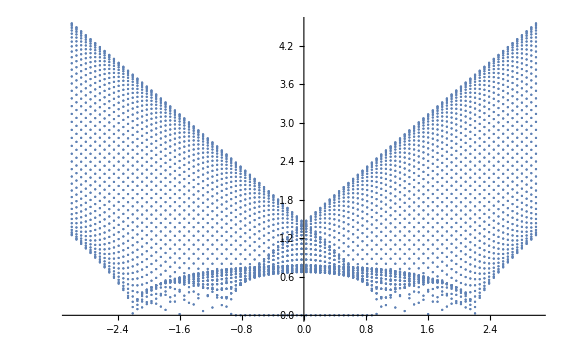

```mathematica
ListPlot[Ess[[3]]]
```

{}

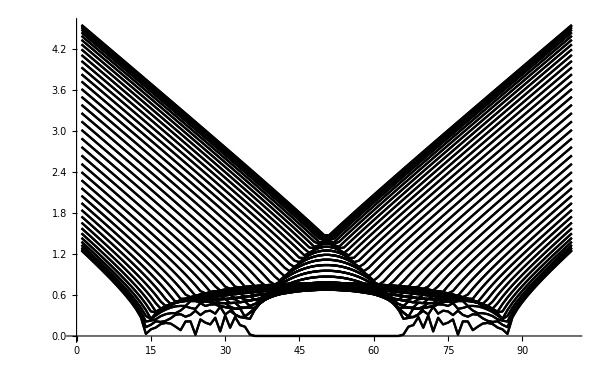

```mathematica
EEp={}
Do[AppendTo[EEp,Abs[EEE[[3]][[All,i]]]],{i,1,2*Nn}]
ListLinePlot[EEp,PlotStyle->Black]
```

```mathematica
RR={}
Do[(R={};
Ei=EE[[i]];
u=U[[i]];

Do[(e=Ei[[j]];
Rr=x/.{ToRules[Roots[v w x^4+((u+g)v+(u-g)w)x^3+(u^2+v^2+w^2-g^2-e^2)x^2+((u+g)w+(u-g)v)x+v w==0,x]]};
Do[AppendTo[R,Rr[[k]]],{k,1,Length[Rr]}]), {j,1,2*Nn}];
AppendTo[RR,N[R]]),{i,1,Length[U]}]
```

{}

```mathematica
Manipulate[ComplexListPlot[RRR[[3]][[i]],PlotStyle->Red,PlotRange->{{-2.5,2.5},{-2,2}}],{i,1,Length[U],1}]
```

Part::partw: Part 91 of {}⟦3⟧ does not exist.

ComplexListPlot::ldata: {}⟦3⟧⟦91⟧ is not a valid dataset or list of datasets.

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 91 of {}⟦3⟧ does not exist.

ComplexListPlot::ldata: {}⟦3⟧⟦91⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification RRR⟦3⟧ is longer than depth of object.

Part::partw: Part 91 of RRR⟦3⟧ does not exist.

ComplexListPlot::ldata: RRR⟦3⟧⟦91⟧ is not a valid dataset or list of datasets.

```mathematica
Mr=Import["raice.csv"]
Mi=Import["raices_imagg_2.csv"]
```

{{-1.06838,-1.06838,0.0753324,11.5614,-1.06838,-1.06838,0.0753324,11.5614,-1.05912,-1.05912,0.0754283,11.5428,296,0.103454,1.15422,1.15422,7.08811,0.103602,1.1654,1.1654,7.06559,0.103602,1.1654,1.1654,7.06559},98,{1}}
 |  |  |  |

{{-0.082122,0.082122,0,0,-0.082122,0.082122,0,0,-0.163789,0.163789,0,0,-0.163789,0.163789,0,0,-0.244547,0.244547,0,0,-0.244547,278,0,0,-0.264552,0.264552,0,0,-0.177462,0.177462,0,0,-0.177462,0.177462,0,0,-0.0890615,0.0890615,0,0,-0.0890615,0.0890615,0},98,{0,318,0}}
 |  |  |  |

```mathematica
Manipulate[(Z=Mr[[i]]+I*Mi[[i]]; ComplexListPlot[Z,PlotRange->{{-2,2},{-2,2}}]),{i,1,100,1}]
```

Part::partd: Part specification Mr⟦100⟧ is longer than depth of object.

Part::partd: Part specification Mi⟦100⟧ is longer than depth of object.

ComplexListPlot::ldata: ⅈ Mi⟦100⟧+Mr⟦100⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification Mr⟦100⟧ is longer than depth of object.

Part::partd: Part specification Mi⟦100⟧ is longer than depth of object.

ComplexListPlot::ldata: ⅈ Mi⟦100⟧+Mr⟦100⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification Mr⟦100⟧ is longer than depth of object.

Part::partd: Part specification Mi⟦100⟧ is longer than depth of object.

ComplexListPlot::ldata: ⅈ Mi⟦100⟧+Mr⟦100⟧ is not a valid dataset or list of datasets.

Part::partd: Part specification Mr⟦100⟧ is longer than depth of object.

Part::partd: Part specification Mi⟦100⟧ is longer than depth of object.

ComplexListPlot::ldata: ⅈ Mi⟦100⟧+Mr⟦100⟧ is not a valid dataset or list of datasets.

```mathematica
Do[Do[Print[i,j],{j,i+1,4}],{i,1,4}]
```

12

13

14

23

24

34

```mathematica
A=Range[-1,1,2/99];
B=Range[-1,1,100];
Manipulate[ContourPlot[x^2/(A[[i]]^2)+y^2==1,{x,-1,1},{y,-1,1}],{i,1,Length[A],1}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification A⟦44⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification A⟦64⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification A⟦15⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
A[[3]]
```

Part::partw: Part 3 of {-1} does not exist.

```mathematica
Manipulate[({u,w}={U[[i]],W[[1]]};
{a,b,c}={v w, (u+g)v+(u-g)w,(u+g)w+(u-g)v};
Z=Mr[[i]]+I*Mi[[i]];
P1=ContourPlot[2 a x(1-(x^2+y^2)^2)-(x^2+y^2)(b(x^2+y^2)-c)==0,{x,-2,2},{y,-2,2}];
P2=ComplexListPlot[Z];
Show[P1,P2]),{i,1,100,1}]
```

Part::partd: Part specification U⟦26⟧ is longer than depth of object.

Part::partd: Part specification W⟦1⟧ is longer than depth of object.

Part::partd: Part specification Mr⟦26⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ComplexListPlot::ldata: ⅈ Mi⟦26⟧+Mr⟦26⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[,ComplexListPlot[ⅈ Mi⟦26⟧+Mr⟦26⟧]].

Part::partd: Part specification U⟦26⟧ is longer than depth of object.

Part::partd: Part specification W⟦1⟧ is longer than depth of object.

Part::partd: Part specification Mr⟦26⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ComplexListPlot::ldata: ⅈ Mi⟦26⟧+Mr⟦26⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[,ComplexListPlot[ⅈ Mi⟦26⟧+Mr⟦26⟧]].

Part::partd: Part specification U⟦26⟧ is longer than depth of object.

Part::partd: Part specification W⟦1⟧ is longer than depth of object.

Part::partd: Part specification Mr⟦26⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ComplexListPlot::ldata: ⅈ Mi⟦26⟧+Mr⟦26⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[,ComplexListPlot[ⅈ Mi⟦26⟧+Mr⟦26⟧]].

Part::partd: Part specification U⟦26⟧ is longer than depth of object.

Part::partd: Part specification W⟦1⟧ is longer than depth of object.

Part::partd: Part specification Mr⟦26⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ComplexListPlot::ldata: ⅈ Mi⟦26⟧+Mr⟦26⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[,ComplexListPlot[ⅈ Mi⟦26⟧+Mr⟦26⟧]].

Part::partd: Part specification U⟦26⟧ is longer than depth of object.

Part::partd: Part specification W⟦1⟧ is longer than depth of object.

Part::partd: Part specification Mr⟦26⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ComplexListPlot::ldata: ⅈ Mi⟦26⟧+Mr⟦26⟧ is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[,ComplexListPlot[ⅈ Mi⟦26⟧+Mr⟦26⟧]].